Logic gates, also known as logical connectives, represent a set of Boolean operations that take in a set number of inputs, which is know as its arity. Within the context of  computer architecture, logical connectives lie at the center point of the industry, enabling digital logic engineers to craft complex systems capable of computation out of simple connectives. Furthermore, within highly transistor efficient computer architectures, the connectives often manifest as “functionally complete,” meaning that the connective can create all other possible connectives solely through compositions with itself. Post’s Functional Completeness Theorem helps narrow down the conditions required for a connective to be functionally complete. The Formula For the Number of Sheffer Functions helps specify the number of functionally complete gates there are of a given arity. Using these two notions, I investigate the conditions in which a connective may appear to be functionally complete, and computationally derive the expressions of all other gates as compositions of a functionally complete one. I then expand this definition to emulate logic/rule-based systems of cellular automata.

## Introduction

Cellular automata are a pattern generated by a set of rules, indicating whether a given cell of a graph will live onto the next generation. Cellular automata (CA) have been used to model population growth, fire spreads, and partial differential equations. There are many different ways in which the rules can manifest. CAs such as Rule 110 and Conway’s Game of Life have rules that are dependent on the presence of other cells. Mathematically, rules are logical expressions. 

Cellular automata offer a visual understanding of what a logical operation does to an initial state. When CA produces eccentric and visually interesting patterns, the process of generating such a pattern is often obscured. After understanding how to backtrack to a rule, a natural extension is to understand how gates of an arity can make up other gates, which may result in more complex rules. This is the notion of functional completeness, which I will expand on later in this essay.

An automata with XOR as a rule, with a following rule plot, or truth table, displaying a self similar pattern:

```mathematica
GraphicsGrid[{{ArrayPlot[CellularAutomaton[{6,2,1/2},{CenterArray[1,10],0},{20,All}],]},{RulePlot[CellularAutomaton[{6,2,1/2}],]}}]
```

-Graphics-

### Exhaustively Finding the Rule of a 2:1 Cellular Automaton

Now this is a square cellular automata governed by a logical expression as a rule. In this specific scenario, the rule is XOR(p, q) for Booleans p, q. The reason I made a custom one and didn’t make use of the in built CellularAutomaton function is because I wanted to specify the input as a Boolean function. The function is iterative, using NestList to find the pattern for future generations.

Defines how to create the next row given a given a previous rule:

```mathematica
nextRow[rule_,offsets_:{1,0}][row_List]:=MapThread[rule,RotateLeft[row,#]&/@offsets];
```

Specify a Boolean automaton function that can be repeated for a certain number of generations, with the ability to specify an offset on what cell to generate

```mathematica
booleanAutomaton[rule_,initialRow_List,steps_Integer,offsets_:{1,0}]:=NestList[nextRow[rule,offsets],initialRow,steps];
```

Initialize a random initial state for the CA to begin with:

```mathematica
randomInitialRow[width_Integer?Positive]:=RandomChoice[{True,False},width];
```

Display the automaton on a grid with a mesh:

```mathematica
displayAutomaton[grid_List]:=ArrayPlot[Boole[grid],];
```

Import the resource function “TruthTable” to visualize truth tables of logical connectives:

```mathematica
truthTable = ResourceFunction["TruthTable"];
```

Truth table of XOR for reference:

```mathematica
truthTable[Xor[a,b], {a,b}]
```

a | b | a⊻b
True | True | False
True | False | True
False | True | True
False | False | False

This is offset here, the first input is the top left and the other is the center to produce a cell under the center.

Define the rule that will be used as well as the output grid to display:

```mathematica
rule=Function[{a,b},Xor[a,b]];

displayAutomaton[booleanAutomaton[rule,randomInitialRow[25],25,{-1,0}]]
```

-Graphics-

I’ve got a cellular automaton based on some logic function (XOR, rule 6) here. The first row is randomized and one can see the development of the pattern. 
The cellular automaton can also be backtracked to decipher the rule that generated it. For example, one would need to find each possible input combination next to each other and map that Boolean output to a truth table. Since I’m are only using gates of arity 2, there is a high chance that I can find all of the possible input conditions within our grid. Similarly, this is easier for 2:1 Boolean logic rules because there are only  possible logic gates of arity 2.

To identify the rule of this automaton, one can find all the input conditions. I could take all the input conditions and create an association to define a rule.

### The Shortcomings of An Exhaustive Approach

For all possible length 10 binary strings, we can find the below distribution of each of the any length 2 binary tuple. Since there are less instances of {1,1} and {0,0}, there must be some binary string of length 10 that cannot be solved when analyzed via the brute force method that I described for classical 2:1 gates. In fact, as the initial state for the cellular automata decreases in length (i.e. the row shrinks in size), the amount of strings that have all 4, length 2 binary string tuples decreases.

Bar chart showing the amount of each possible length 2 binary input occurs within all tuples of length 10:

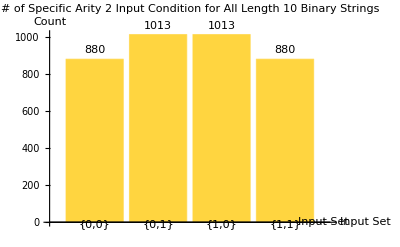

```mathematica
BarChart[Dataset[AssociationThread[Tuples[{0,1},2]->Table[Count[Tuples[{0,1},10],str_/;MemberQ[Partition[str,2,1],tuple]],{tuple,Tuples[{0,1},2]}]]
], , ]
```

Plot displaying the count of how many length 10 binary strings contain a certain amount of the total possible amount of binary inputs:

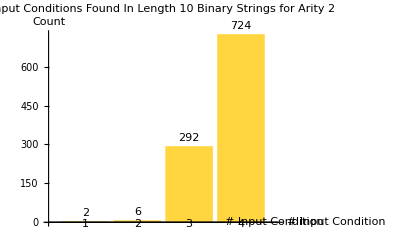

```mathematica
BarChart[Dataset[Counts[Length[DeleteDuplicates[Partition[#,2,1]]]&/@Tuples[{0,1},10]]],, ]
```

For initial binary string of length 10, there are 724 possible configurations that contain all 4 of the possible inputs. Therefore, the brute force method would apply to those types of strings. However, this is not generalizable to all initial states. As the length of the initial row decreases, there are less combinations that contain all 4 strings. Eventually, once the size of the initial state is length 4 or below, it becomes impossible for all 4 input conditions to coexist.

Grid of a number of plots showing how it becomes more difficult to find all possible input conditions as the size of the initial conditions decrease:

```mathematica
createChart[length_]:=With[{counts=Counts[Length[DeleteDuplicates[Partition[#,2,1]]]&/@Tuples[{0,1},length]]},BarChart[KeySort[counts],ChartLabels->Placed[Keys[KeySort[counts]],Below],]]
```

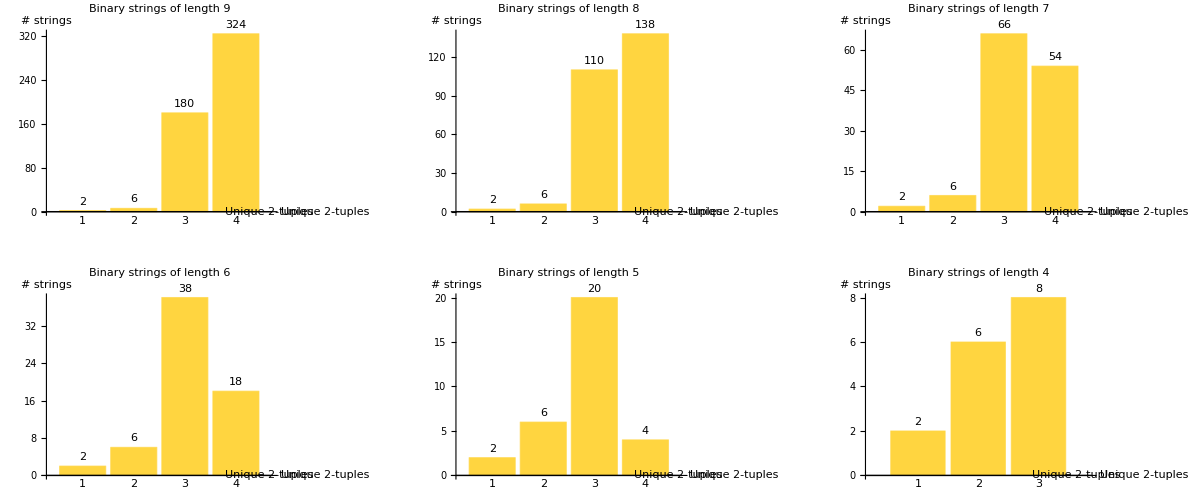

```mathematica
GraphicsGrid[Partition[Table[createChart[length],{length,9,4, -1}],3], ]
```

Likewise, if I increase the arity of our logical rule, we need to be able to find the exact input conditions that created that cellular automaton. Since there are  cells that are considered when evaluating the input, it becomes unlikely to find that exact input condition. In fact, the possible conditions scale by , further showing that an exhaustive approach is difficult. An interesting application of this property of cellular automata is within the field of cybersecurity. There are security products that rely on scalable encryption. Since backtracking to find the pattern of an arity  gate is a difficult problem, it’s used in hashing algorithms due to their complex behavior emerging from simple rules. In order to gain some insight into how these types of rules may be generated, let’s explore the idea of functional completeness, establishing how rules may be composed within each other to create other rules, thus simplifying them.

## Finding a Functionally Complete Gate

For 3 :1 gates, there are  possible logic gates, each of which corresponding with a unique output of a truth table. It is important to note that many of them, analogous to 2:1 gates, can be made from a composition of other gates. I don’t think that all 256 of these gates have their own name.

### Checking With Post’s Functional Completeness Theorem

A function is denoted functionally complete if it fails to exhibit all 5 of these conditions.

Preserving 0: if all inputs are 0, the output must be 0

Preserving 1: if all inputs are 1, the output must be 1

Linearity: inverting an input either always changes the output or never does

Monotonicity: increasing the inputs (0→1) must never make the output decrease(1→0)

Self-Duality: if all the inputs are inverted, the output should also be inverted

### Why NAND is Functionally Complete

Consider NAND, a functionally complete gate. The truth table of a 2:1 NAND gate is:

Truth table for a 2 input NAND gate for reference:

```mathematica
truthTable[Nand[p,q], {p,q}]
```

p | q | p⊼q
True | True | False
True | False | True
False | True | True
False | False | True

NAND aptly fails all 5 of Post’s conditions.

Preserving 0:

When the input is (0,0), the output is 1. So NAND fails this condition.

Preserving 1:

When the input is (1,1), the output is 0. So NAND fails this condition.

Linearity

When the input is (1,1), the output is 0. However, when the input is (1,0), the output is 1. But, when the input is (0,1), the output is also 1. So NAND fails this condition.

Monotonicity

When the inputs go from (0,0) to (1,1), the output decreases from 1 to 0. So NAND fails this condition.

Self-Duality

When the inputs are changed from (1,0) to (0,1) via bitwise inversion, the output does not change. So NAND fails this condition.

### An Important Equation

It has been proven that  is the formula that represents the amount of functionally complete gates for arity . Before I begin exploring 3:1 gates, I’ll need to show how many functionally complete 3:1 gates there actually are. According to the formula, there should be 56 functionally complete 3:1 gates.

Filters for failures in Post’s conditions for all length 8 binary strings, explicitly checking preserving and linearity rules:

```mathematica
isLinear[truthTable_List]:=FreeQ[BooleanConvert[BooleanFunction[truthTable//Reverse],"ANF"],And]
isMonotonic[truthTable_List]:=FreeQ[BooleanConvert[BooleanFunction[truthTable//Reverse],"DNF"],Not]
isFunctionallyComplete[t_List]:=Not[First[t]==0||Last[t]==1||isLinear[t]||isMonotonic[t]||t==(1-Reverse[t])]
```

Find all functionally complete gates of arity 3:

```mathematica
completeTables=Select[Tuples[{0,1},8],isFunctionallyComplete]
```

{{1,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0},{1,0,0,0,0,1,0,0},{1,0,0,0,0,1,1,0},{1,0,0,0,1,0,0,0},{1,0,0,0,1,0,1,0},{1,0,0,0,1,1,0,0},{1,0,0,1,0,0,0,0},{1,0,0,1,0,0,1,0},{1,0,0,1,0,1,0,0},{1,0,0,1,1,0,0,0},{1,0,0,1,1,0,1,0},{1,0,0,1,1,1,0,0},{1,0,0,1,1,1,1,0},{1,0,1,0,0,0,0,0},{1,0,1,0,0,0,1,0},{1,0,1,0,0,1,0,0},{1,0,1,0,0,1,1,0},{1,0,1,0,1,0,0,0},{1,0,1,0,1,1,0,0},{1,0,1,0,1,1,1,0},{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,0,1,1,0,1,1,0},{1,0,1,1,1,0,0,0},{1,0,1,1,1,0,1,0},{1,0,1,1,1,1,0,0},{1,0,1,1,1,1,1,0},{1,1,0,0,0,0,0,0},{1,1,0,0,0,0,1,0},{1,1,0,0,0,1,0,0},{1,1,0,0,0,1,1,0},{1,1,0,0,1,0,0,0},{1,1,0,0,1,0,1,0},{1,1,0,0,1,1,1,0},{1,1,0,1,0,0,0,0},{1,1,0,1,0,0,1,0},{1,1,0,1,0,1,1,0},{1,1,0,1,1,0,0,0},{1,1,0,1,1,0,1,0},{1,1,0,1,1,1,0,0},{1,1,0,1,1,1,1,0},{1,1,1,0,0,0,0,0},{1,1,1,0,0,0,1,0},{1,1,1,0,0,1,0,0},{1,1,1,0,0,1,1,0},{1,1,1,0,1,0,1,0},{1,1,1,0,1,1,0,0},{1,1,1,0,1,1,1,0},{1,1,1,1,0,0,1,0},{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,0,1,0},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,0}}

Convert all of the functionally complete truth tables into  a rule for a cellular automata:

```mathematica
completeArity3CAs=Select[Tuples[{0,1},8],isFunctionallyComplete]//Map[FromDigits[#,2]&]
```

{128,130,132,134,136,138,140,144,146,148,152,154,156,158,160,162,164,166,168,172,174,176,180,182,184,186,188,190,192,194,196,198,200,202,206,208,210,214,216,218,220,222,224,226,228,230,234,236,238,242,244,246,248,250,252,254}

The following cellular automata are made up of functionally complete rules. Since each of these are each 3:1, they can even be composed within themselves in some manner to produce the famous, Turing-complete, Rule 110!

All 56 functionally complete cellular automata expressed aged 20 generations from a common initial position:

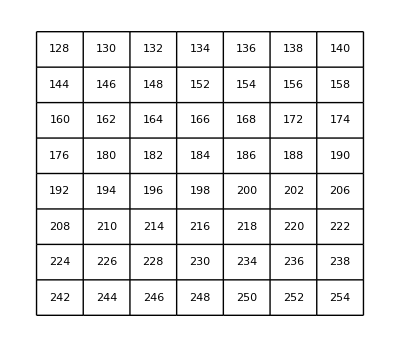

```mathematica
completeArity3CAs//Map[Column[{#,RulePlot[CellularAutomaton[#], ImageSize->143],ArrayPlot[CellularAutomaton[#,{{1},0},{20,All}]]}]&]//Partition[#,7,7,1,{}]&//GraphicsGrid[#, , ]&
```

Rule 110 for reference, any of the above automatons can generate this via composition alone:

```mathematica
GraphicsColumn[{ArrayPlot[CellularAutomaton[110,{{1},0},150], ], RulePlot[CellularAutomaton[110], ]}, ]
```

-Graphics-

## Defining How To Compose Functions

To find all of the possible compositions, I employed a recursive function to find all of the open spots within a function of a set arity and replace each input with another function depending on a specified depth. This is a brute force approach of finding all of the possible compositions of functions. At first, there was difficulty in computing, but after employing a couple of tricks, I drastically improved the computation speed by vastly reducing the space at which the function has to recurse. This function works by establishing a basis of 3 variables, and then repeatedly placing each of them in all combinations within the a specified function. This approach rapidly increases the space of all compositions that I am keeping track of.

Load in the InverseBoole resource function for ease of use:

```mathematica
inverseBoole = ResourceFunction["InverseBoole"]
```

Creates an association between the inputs and outputs of a logic gate:

```mathematica
makeExplicitRule[truthTable_List] := AssociationThread[Tuples[{False, True},Log2[Length[truthTable]]], truthTable];
```

Recursive algorithm to find all compositions of a truth table with itself:

```mathematica
termsUpToDepth[vars_List,head_,0]:=vars;

termsUpToDepth[vars_List,head_,d_Integer?Positive]:=termsUpToDepth[vars,head,d]=DeleteDuplicates[Join[vars,Flatten[Table[head[x,y,z],{x,termsUpToDepth[vars,head,d-1]},{y,termsUpToDepth[vars,head,d-1]},{z,termsUpToDepth[vars,head,d-1]}],2]]];
```

Recursive algorithm to find all compositions of a truth table with itself (for binary... less computationally expensive):

```mathematica
termsUpToDepthBi[vars_List,head_,0]:=vars;

termsUpToDepthBi[vars_List,head_,d_Integer?Positive]:=termsUpToDepthBi[vars,head,d]=Join[vars,Flatten[Table[head[x,y],{x,termsUpToDepthBi[vars,head,d-1]},{y,termsUpToDepthBi[vars,head,d-1]}],2]];
```

## Finding Compositions

### Test With Arity n = 2

To be able to find the most “reduced” functional expression, I need an algorithm that finds all of the compositions of a function of a given arity and checks all of the unique truth tables that they produce. I will start by creating some helper functions, and then move onto applying this to gates of arity 2. It is known that the 2 functionally complete connectives of arity 2 are NAND and NOR.

Confirming that our checks with Post’s Theorem finds NAND and NOR as functionally complete. Each of these are the DeMorganized outputs of NAND and NOR:

```mathematica
BooleanFunction[makeExplicitRule[Select[Tuples[{0,1},4], isFunctionallyComplete][[2]]]//inverseBoole//Normal, {p,q}]
```

!p||!q

```mathematica
BooleanFunction[makeExplicitRule[Select[Tuples[{0,1},4], isFunctionallyComplete][[1]]]//inverseBoole//Normal, {p,q}]
```

!p&&!q

Create a logical association between all inputs and defined outputs:

```mathematica
functionRuleForm[truthtable_]:=Normal[AssociationThread[f@@@Tuples[{0,1},2],truthtable]]
```

Finds a certain term within the space of all compositions of the function f:

```mathematica
termToTruthTable[n_Integer, functionYouTest_List]:=(termsUpToDepthBi[{p,q},f,3][[n]]//. {p->#[[1]], q->#[[2]]}&/@Tuples[{0,1},2])//. functionRuleForm[functionYouTest]
```

NAND has been exhaustively shown to be functionally complete using our function! Since it returns all 16 possible truth table outputs for arity 2, all possible 2:1 functions can be modeled by NAND.

Shows all truth tables that a given truth table, in this case {1, 1, 1, 0} (aka NAND) can create from compositions with itself:

```mathematica
DeleteDuplicates[Table[termToTruthTable[n, {1,1,1,0}],{n,1,Length[termsUpToDepthBi[{p,q},f,3]]}]]
```

{{0,0,1,1},{0,1,0,1},{1,1,0,0},{1,1,1,0},{1,1,1,1},{1,1,0,1},{1,0,1,0},{1,0,1,1},{0,1,1,1},{0,0,0,1},{1,0,0,1},{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,1,1,0}}

This is a similar case for NOR. Like NAND, it also returns all 16 logic gates which proves that it’s functionally complete.

Shows all truth tables that a given truth table, in this case {1, 0, 0, 0} (aka NOR) can create from compositions with itself:

```mathematica
DeleteDuplicates[Table[termToTruthTable[n, {1,0,0,0}],{n,1,Length[termsUpToDepthBi[{p,q},f,3]]}]]
```

{{0,0,1,1},{0,1,0,1},{1,1,0,0},{1,0,0,0},{0,0,0,0},{0,1,0,0},{1,0,1,0},{0,0,1,0},{0,0,0,1},{0,1,1,1},{0,1,1,0},{1,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0},{1,0,0,1}}

Creates a grid of all the compositions of NOR with itself to produce every arity 2 logic gate in increasing binary order from left to right:

```mathematica
Labeled[Grid[Partition[Reverse[DeleteDuplicates[AssociationThread[termsUpToDepthBi[{p,q},f,3],Table[termToTruthTable[n, {1,0,0,0}],{n,1,Length[termsUpToDepthBi[{p,q},f,3]]}]]]]//Sort//Keys,4], Frame->All],"Compositions of f=NOR With Itself To Produce All Gates of Arity 2", Bottom]
```

f[p,f[p,p]] | f[f[p,p],f[q,q]] | f[q,f[p,p]] | p
f[p,f[p,q]] | q | f[f[p,q],f[f[p,p],f[q,q]]] | f[f[p,q],f[p,q]]
f[p,q] | f[f[p,f[p,q]],f[q,f[p,p]]] | f[q,q] | f[f[p,f[p,p]],f[p,f[p,q]]]
f[p,p] | f[f[p,f[p,p]],f[q,f[p,p]]] | f[f[p,f[p,p]],f[f[p,p],f[q,q]]] | f[f[p,f[p,p]],f[p,f[p,p]]]Compositions of f=NOR With Itself To Produce All Gates of Arity 2

However, for some other random logic gate, this is not the case. Consider a truth expression which I randomly chose: {1,0,0,1}. Since it can only 4/16 of the connectives, it fails to be functionally complete, thus verifying that implementing Post’s functional completeness theorem works well to narrow down which gates satisfy functional completeness.

```mathematica
DeleteDuplicates[Table[termToTruthTable[n, {1,0,0,1}],{n,1,Length[termsUpToDepthBi[{p,q},f,3]]}]]
```

{{0,0,1,1},{0,1,0,1},{1,1,1,1},{1,0,0,1}}

Creates a grid of all the compositions of NAND with itself to produce every arity 2 logic gate in increasing binary order from left to right:

```mathematica
Labeled[Grid[Partition[Reverse[DeleteDuplicates[AssociationThread[termsUpToDepthBi[{p,q},f,3],Table[termToTruthTable[n, {1,1,1,0}],{n,1,Length[termsUpToDepthBi[{p,q},f,3]]}]]]]//Sort//Keys,4], ],"Compositions of f=NAND With Itself To Produce All Gates of Arity 2", Bottom]
```

f[f[p,f[p,p]],f[p,f[p,p]]] | f[f[p,q],f[p,q]] | f[f[p,f[p,p]],f[p,f[p,q]]] | p
f[f[p,f[p,p]],f[q,f[p,p]]] | q | f[f[p,f[p,q]],f[q,f[p,p]]] | f[f[p,p],f[q,q]]
f[f[p,f[p,p]],f[f[p,p],f[q,q]]] | f[f[p,q],f[f[p,p],f[q,q]]] | f[q,q] | f[q,f[p,p]]
f[p,p] | f[p,f[p,q]] | f[p,q] | f[p,f[p,p]]Compositions of f=NAND With Itself To Produce All Gates of Arity 2

People often hear that NAND is a more “efficient” gate than NOR. In fact, within computer engineering, it is, but within the lens of functional completeness, they perform quite similarly. I’m measuring efficiency by the depth needed to generate a logic gate. This is because there is more computation involved to reach find the output of a logic gate that has many nested gates within itself. The mean depth required to generate all 16 connectives for arity 2 are the same. However, I’ll define a tiebreaker as the connective that has less higher depth gates. 

NOR appears to have less depth 3 connectives than NAND, so therefore it would mean that it is more “efficient”:

```mathematica
makeTable[title_,data_]:=Column[{Style[title,Bold,18],Grid[data,]},]

Grid[{{makeTable["NAND",{{"Depth","Count"},{1,4},{2,5},{3,7}}],makeTable["NOR",{{"Depth","Count"},{1,5},{2,5},{3,6}}]}},]
```

NAND
Depth | Count
1 | 4
2 | 5
3 | 7 | NOR
Depth | Count
1 | 5
2 | 5
3 | 6

All 2:1 gates in terms of f=NAND displayed as tree graphs:

```mathematica
truthTableToExpression = DeleteDuplicates[AssociationThread[termsUpToDepthBi[{p,q},f,3],Table[termToTruthTable[n,{1,1,1,0}],{n,1,Length[termsUpToDepthBi[{p,q},f,3]]}]]];
```

```mathematica
Grid[Partition[TreeForm[#,]&/@Keys[Sort[Reverse[truthTableToExpression]]],4],]
```

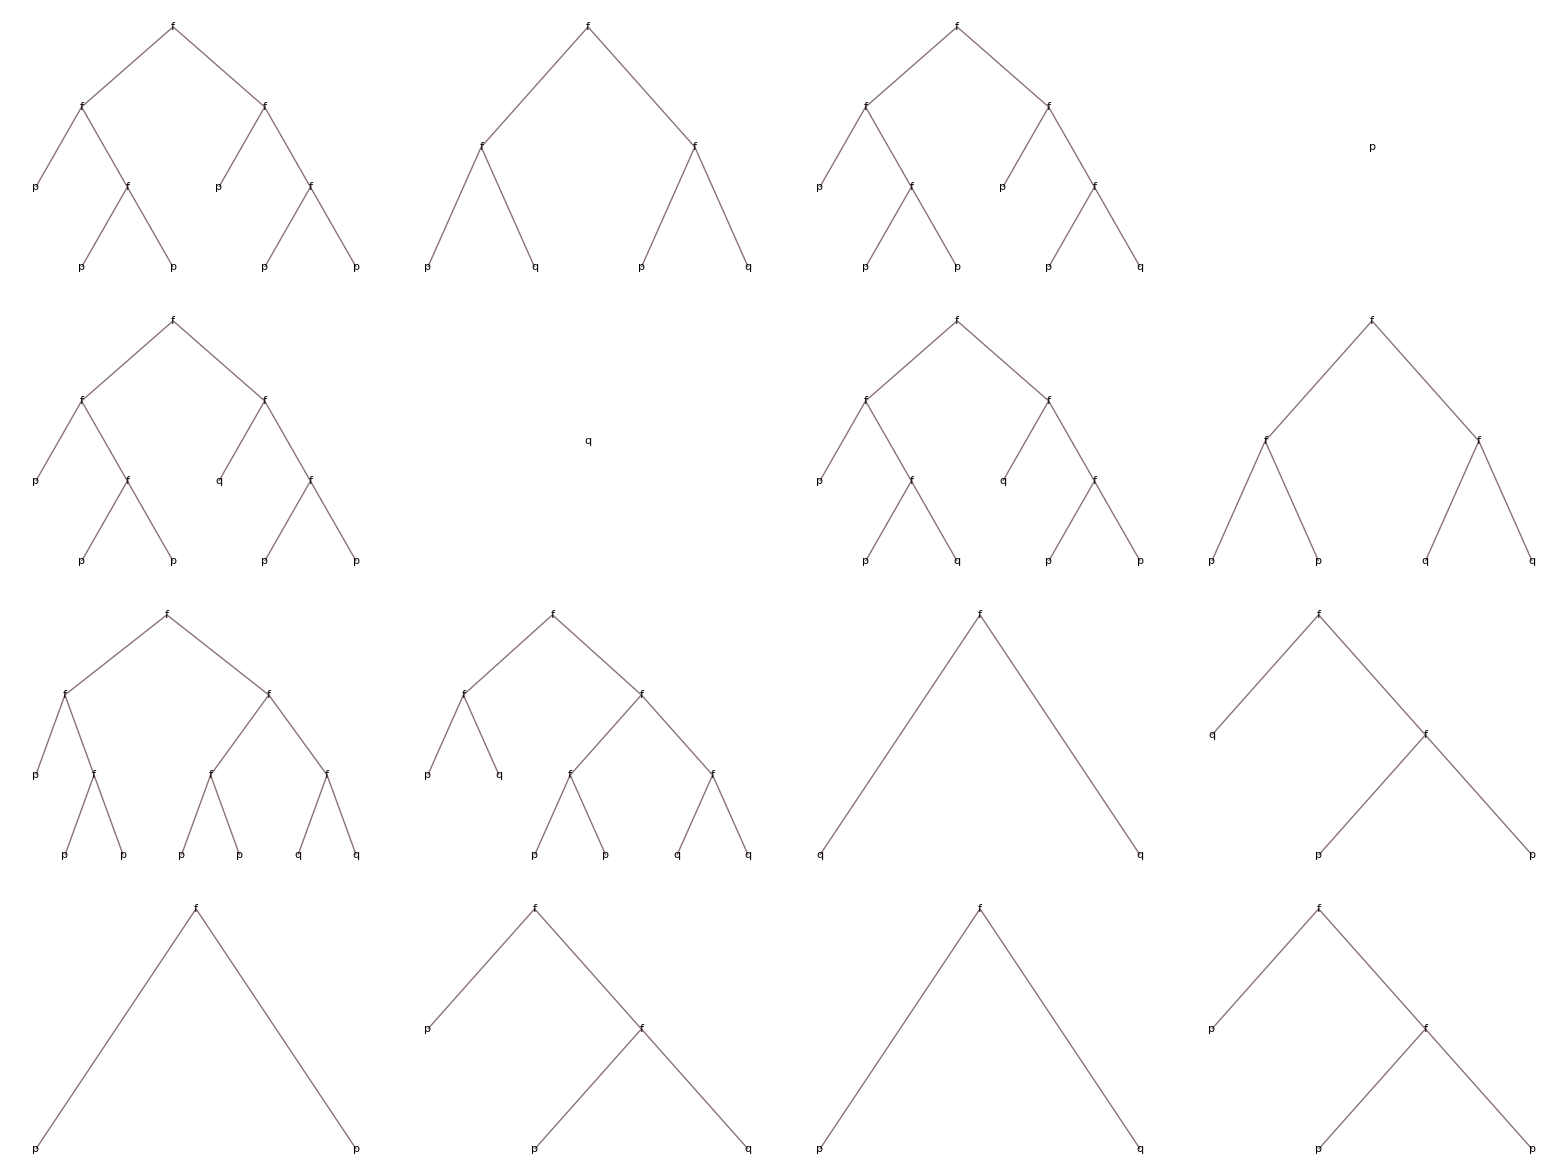

### Expansion to Arity n = 3

This recursive composition approach is effective but hits a couple of roadblocks. For NAND, it is only able to generate 250 of the tuples, meaning it overlooks 6 tuples that are important. My theory is that there are a couple of gates that have depth 4. Also, for “efficient” gates (ex: the one Christopher Wolfram showed), since there are more gates that match unique truth tables found in depth 2. This means that the space that depth 3 and 4 needs to search is much larger, rapidly increasing the number of combination that the algorithm needs to search for.

Converts a functional expression into a truth table:

```mathematica
termToTruthTable[n_Integer]:=(termsUpToDepthBi[{p,q},f,3][[n]]//. {p->#[[1]], q->#[[2]]}&/@Tuples[{0,1},2])//. functionRuleForm[{1,0,0,0}]
```

Deletes the duplicate elements that are present in a generated set of expressions:

```mathematica
DeleteDuplicates[Table[termToTruthTable[n],{n,1,Length[termsUpToDepthBi[{p,q},f,3]]}]]
```

{{0,0,1,1},{0,1,0,1},{1,1,0,0},{1,0,0,0},{0,0,0,0},{0,1,0,0},{1,0,1,0},{0,0,1,0},{0,0,0,1},{0,1,1,1},{0,1,1,0},{1,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0},{1,0,0,1}}

Creates an association between the possible inputs and outputs of a function:

```mathematica
functionRuleForm[truthtable_]:=Normal[AssociationThread[f@@@Tuples[{0,1},Log2[Length[truthtable]]],truthtable]]
```

Creates a truth table based on a functional term, specifying NAND as a rule:

```mathematica
termToTruthTable[term_]:=(term//.{p->#[[1]],q->#[[2]],r->#[[3]]}&/@Tuples[{0,1},3])//.functionRuleForm[{1,1,1,1,1,1,1,0}]
```

Find all depth 2, 3:1 gates. Note, this can take several minutes:

```mathematica
depthTwoTernary=termsUpToDepth[{p,q,r},f,2];
```

Collect all equivalent terms into their own class, since many of the compositions are redundant and equivalent when evaluated:

```mathematica
equivTerms1=GatherBy[depthTwoTernary,termToTruthTable];
```

Collect the first element of each equivalence class, because that’s the most efficient functionally expression (least depth):

```mathematica
testSet = #[[1]]&/@equivTerms1;
```

The algorithm to place expressions in every argument position of expressions of higher depth:

```mathematica
termsUpToDepthStep[vars_List,head_,0]:=vars;
termsUpToDepthStep[vars_List,head_,d_Integer?Positive]:=termsUpToDepthStep[vars,head,d]=Join[vars,Flatten[Table[head[p,q,r],{p,termsUpToDepthStep[vars,head,d-1]},{q,termsUpToDepthStep[vars,head,d-1]}, {r,termsUpToDepthStep[vars,head,d-1]}],2]];
```

Repeat the process of increasing the depth of the expressions that was  already derived in testSet (very narrowed down functional space):

```mathematica
depthThreeTernary = termsUpToDepthStep[testSet, f, 1];
```

Again, gather the newly generated terms into their own equivalence class:

```mathematica
equivTerms2=GatherBy[depthThreeTernary,termToTruthTable];
```

Again, take the first expression of each equivalence class and compile into a final list:

```mathematica
testSet2 = #[[1]]&/@equivTerms2;
```

Oh no! There’s only 250 and not 256:

Finds the length of all the expressions that were found

```mathematica
termToTruthTable/@testSet2//Length
```

250

## An Alternative Approach To Nested Compositions

Since the previous approach to finding the compositions did not suffice, I’ll have to adopt a more rigorous approach. This approach directly composes truth tables within itself to generate a new truth table, and then checks if that truth table is novel. Repeating this over time, means that it should output 256 compositions, regardless of their efficiency due to FixedPoint. I got all 256 compositions here.

Converts a truth table to a binary string:

```mathematica
ttKey[tt_List]:=StringJoin[ToString/@tt];
```

Composes 3 truth tables within itself to get a resultant connective:

```mathematica
compose3[gateTT_List,uTT_List,vTT_List,wTT_List]:=gateTT[[1+FromDigits[#,2]]]&/@Transpose[{uTT,vTT,wTT}];
```

The initial terms that helps initiate the composition process:

```mathematica
initialTerms[]:=With[{rows=Tuples[{0,1},3]},{<|"Term"->p,"TT"->rows[[All,1]]|>,<|"Term"->q,"TT"->rows[[All,2]]|>,<|"Term"->r,"TT"->rows[[All,3]]|>}]
```

Creates an association between the terms and the truth tables, for easier navigation later:

```mathematica
composeTermTriple[gateTT_,gateSymbol_][{u_,v_,w_}]:=<|"Term"->gateSymbol[u["Term"],v["Term"],w["Term"]],"TT"->compose3[gateTT,u["TT"],v["TT"],w["TT"]]|>;
```

Generates new terms using the compostTermTriple function:

```mathematica
newTermsFrom[gateTT_,gateSymbol_][terms_List]:=composeTermTriple[gateTT,gateSymbol]/@Tuples[terms,3];
```

Adds the new association to a growing term list:

```mathematica
addNewTerms[gateTT_,gateSymbol_][terms_List]:=With[{seenKeys=ttKey/@terms[[All,"TT"]],candidates=newTermsFrom[gateTT,gateSymbol][terms]},Join[terms,DeleteDuplicatesBy[Select[candidates,!MemberQ[seenKeys,ttKey[#["TT"]]]&],ttKey[#["TT"]]&]]];
```

Continuously add new terms, growing from the initial terms until it is no longer possible to make more connectives (limit is 256 for arity 3):

```mathematica
novelTermsClosure[gateTT_List,gateSymbol_:g]:=FixedPoint[addNewTerms[gateTT,gateSymbol],initialTerms[]];
```

The function compositions for 3:1 NAND, which have previously shown to be functionally complete. Note: this can take several minutes:

```mathematica
composedTerms = novelTermsClosure[{1,1,1,1,1,1,1,0}];
```

{<|Term→x,TT→{0,0,0,0,1,1,1,1}|>,<|Term→y,TT→{0,0,1,1,0,0,1,1}|>,<|Term→z,TT→{0,1,0,1,0,1,0,1}|>,<|Term→f[x,x,x],TT→{1,1,1,1,0,0,0,0}|>,<|Term→f[x,x,y],TT→{1,1,1,1,1,1,0,0}|>,<|Term→f[x,x,z],TT→{1,1,1,1,1,0,1,0}|>,<|Term→f[x,y,z],TT→{1,1,1,1,1,1,1,0}|>,<|Term→f[y,y,y],TT→{1,1,0,0,1,1,0,0}|>,<|Term→f[y,y,z],TT→{1,1,1,0,1,1,1,0}|>,<|Term→f[z,z,z],TT→{1,0,1,0,1,0,1,0}|>,<|Term→f[x,x,f[x,x,x]],TT→{1,1,1,1,1,1,1,1}|>,<|Term→f[x,x,f[x,x,y]],TT→{1,1,1,1,0,0,1,1}|>,<|Term→f[x,x,f[x,x,z]],TT→{1,1,1,1,0,1,0,1}|>,<|Term→f[x,x,f[x,y,z]],TT→{1,1,1,1,0,0,0,1}|>,<|Term→f[x,y,f[x,x,z]],TT→{1,1,1,1,1,1,0,1}|>,<|Term→f[x,z,f[x,x,y]],TT→{1,1,1,1,1,0,1,1}|>,<|Term→f[x,f[x,x,y],f[x,x,z]],TT→{1,1,1,1,0,1,1,1}|>,<|Term→f[y,y,f[x,x,x]],TT→{1,1,0,0,1,1,1,1}|>,<|Term→f[y,y,f[x,x,z]],TT→{1,1,0,0,1,1,0,1}|>,<|Term→f[y,y,f[y,y,z]],TT→{1,1,0,1,1,1,0,1}|>,<|Term→f[y,z,f[x,x,x]],TT→{1,1,1,0,1,1,1,1}|>,<|Term→f[y,f[x,x,x],f[y,y,z]],TT→{1,1,0,1,1,1,1,1}|>,<|Term→f[z,z,f[x,x,x]],TT→{1,0,1,0,1,1,1,1}|>,<|Term→f[z,z,f[x,x,y]],TT→{1,0,1,0,1,0,1,1}|>,<|Term→f[z,z,f[y,y,y]],TT→{1,0,1,1,1,0,1,1}|>,<|Term→f[z,f[x,x,x],f[y,y,y]],TT→{1,0,1,1,1,1,1,1}|>,<|Term→f[f[x,x,x],f[x,x,x],f[y,y,y]],TT→{0,0,1,1,1,1,1,1}|>,<|Term→f[f[x,x,x],f[x,x,x],f[y,y,z]],TT→{0,0,0,1,1,1,1,1}|>,<|Term→f[f[x,x,x],f[x,x,x],f[z,z,z]],TT→{0,1,0,1,1,1,1,1}|>,<|Term→f[f[x,x,x],f[y,y,y],f[z,z,z]],TT→{0,1,1,1,1,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[x,x,y]],TT→{0,0,0,0,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[x,x,z]],TT→{0,0,0,0,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[y,y,z]],TT→{0,0,0,1,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[z,z,z]],TT→{0,1,0,1,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,z],f[y,y,y]],TT→{0,0,1,1,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,z],f[y,y,z]],TT→{0,0,0,1,0,1,1,1}|>,<|Term→f[f[x,x,y],f[y,y,y],f[z,z,z]],TT→{0,1,1,1,0,1,1,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[x,x,z]],TT→{0,0,0,0,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[y,y,z]],TT→{0,0,0,1,0,1,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[x,y,z]],TT→{0,0,0,0,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[y,y,z]],TT→{0,0,0,1,0,0,0,1}|>,<|Term→f[x,x,f[x,y,f[x,x,z]]],TT→{1,1,1,1,0,0,1,0}|>,<|Term→f[x,x,f[x,z,f[x,x,y]]],TT→{1,1,1,1,0,1,0,0}|>,<|Term→f[x,x,f[x,f[x,x,y],f[x,x,z]]],TT→{1,1,1,1,1,0,0,0}|>,<|Term→f[x,f[x,y,z],f[x,f[x,x,y],f[x,x,z]]],TT→{1,1,1,1,1,0,0,1}|>,<|Term→f[x,f[x,y,f[x,x,z]],f[x,z,f[x,x,y]]],TT→{1,1,1,1,0,1,1,0}|>,<|Term→f[y,y,f[x,x,f[x,x,z]]],TT→{1,1,0,0,1,1,1,0}|>,<|Term→f[y,y,f[y,z,f[x,x,x]]],TT→{1,1,0,1,1,1,0,0}|>,<|Term→f[y,y,f[y,f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,1,1,0,0}|>,<|Term→f[y,f[x,x,z],f[y,f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,1,1,0,1}|>,<|Term→f[y,f[x,x,f[x,x,z]],f[y,z,f[x,x,x]]],TT→{1,1,0,1,1,1,1,0}|>,<|Term→f[z,z,f[x,x,f[x,x,y]]],TT→{1,0,1,0,1,1,1,0}|>,<|Term→f[z,z,f[y,y,f[x,x,x]]],TT→{1,0,1,1,1,0,1,0}|>,<|Term→f[z,z,f[z,f[x,x,x],f[y,y,y]]],TT→{1,1,1,0,1,0,1,0}|>,<|Term→f[z,f[x,x,y],f[z,f[x,x,x],f[y,y,y]]],TT→{1,1,1,0,1,0,1,1}|>,<|Term→f[z,f[x,x,f[x,x,y]],f[y,y,f[x,x,x]]],TT→{1,0,1,1,1,1,1,0}|>,<|Term→f[f[x,x,x],f[x,x,x],f[y,y,f[y,y,z]]],TT→{0,0,1,0,1,1,1,1}|>,<|Term→f[f[x,x,x],f[x,x,x],f[z,z,f[y,y,y]]],TT→{0,1,0,0,1,1,1,1}|>,<|Term→f[f[x,x,x],f[x,x,x],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,1,1,1,1}|>,<|Term→f[f[x,x,x],f[y,y,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,1,1,1,1}|>,<|Term→f[f[x,x,x],f[y,y,f[y,y,z]],f[z,z,f[y,y,y]]],TT→{0,1,1,0,1,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[x,x,f[x,x,z]]],TT→{0,0,0,0,1,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[y,y,f[y,y,z]]],TT→{0,0,1,0,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[z,z,f[x,x,x]]],TT→{0,1,0,1,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[z,z,f[y,y,y]]],TT→{0,1,0,0,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,0,0,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[f[x,x,x],f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,0,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[f[x,x,y],f[x,x,z],f[y,y,y]]],TT→{1,1,0,0,1,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[f[x,x,y],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,1,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,z],f[y,y,f[y,y,z]]],TT→{0,0,1,0,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,z],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,z],f[f[x,x,x],f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,z],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,0,1,1,1}|>,<|Term→f[f[x,x,y],f[y,y,y],f[x,x,f[x,x,z]]],TT→{0,0,1,1,1,0,1,1}|>,<|Term→f[f[x,x,y],f[y,y,y],f[z,z,f[x,x,x]]],TT→{0,1,1,1,0,0,1,1}|>,<|Term→f[f[x,x,y],f[y,y,y],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,0,0,1,1}|>,<|Term→f[f[x,x,y],f[y,y,z],f[x,x,f[x,x,z]]],TT→{0,0,0,1,1,0,1,1}|>,<|Term→f[f[x,x,y],f[y,y,z],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,0,0,1,1}|>,<|Term→f[f[x,x,y],f[y,y,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,0,0,1,1}|>,<|Term→f[f[x,x,y],f[y,y,z],f[f[x,x,y],f[x,x,z],f[y,y,y]]],TT→{1,1,0,1,1,0,1,1}|>,<|Term→f[f[x,x,y],f[y,y,z],f[f[x,x,y],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,1,0,1,1}|>,<|Term→f[f[x,x,y],f[z,z,z],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,0,1,1,1}|>,<|Term→f[f[x,x,y],f[x,x,f[x,x,z]],f[y,y,f[y,y,z]]],TT→{0,0,1,0,1,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,f[x,x,z]],f[z,z,f[x,x,x]]],TT→{0,1,0,1,1,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,f[x,x,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,0,0,1,0,1,1}|>,<|Term→f[f[x,x,y],f[y,y,f[y,y,z]],f[z,z,f[y,y,y]]],TT→{0,1,1,0,0,1,1,1}|>,<|Term→f[f[x,x,y],f[y,y,f[y,y,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,1,0,0,0,1,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[x,x,f[x,x,y]]],TT→{0,0,0,0,1,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[y,y,f[x,x,x]]],TT→{0,0,1,1,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[y,f[x,x,x],f[y,y,z]]],TT→{0,0,1,0,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[z,z,f[y,y,y]]],TT→{0,1,0,0,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[f[x,x,x],f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[f[x,x,y],f[x,x,y],f[z,z,z]]],TT→{1,0,1,0,1,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[f[x,x,y],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,1,1,0,1}|>,<|Term→f[f[x,x,z],f[y,y,y],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,0,1,1,1}|>,<|Term→f[f[x,x,z],f[y,y,z],f[x,x,f[x,x,y]]],TT→{0,0,0,1,1,1,0,1}|>,<|Term→f[f[x,x,z],f[y,y,z],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,0,1,0,1}|>,<|Term→f[f[x,x,z],f[y,y,z],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,0,1,0,1}|>,<|Term→f[f[x,x,z],f[y,y,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,0,1,0,1}|>,<|Term→f[f[x,x,z],f[y,y,z],f[f[x,x,y],f[x,x,y],f[z,z,z]]],TT→{1,0,1,1,1,1,0,1}|>,<|Term→f[f[x,x,z],f[y,y,z],f[f[x,x,y],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,1,1,0,1}|>,<|Term→f[f[x,x,z],f[z,z,z],f[x,x,f[x,x,y]]],TT→{0,1,0,1,1,1,0,1}|>,<|Term→f[f[x,x,z],f[z,z,z],f[y,y,f[x,x,x]]],TT→{0,1,1,1,0,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,f[x,x,y]],f[y,y,f[x,x,x]]],TT→{0,0,1,1,1,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,f[x,x,y]],f[y,f[x,x,x],f[y,y,z]]],TT→{0,0,1,0,1,1,0,1}|>,<|Term→f[f[x,x,z],f[x,x,f[x,x,y]],f[z,z,f[y,y,y]]],TT→{0,1,0,0,1,1,0,1}|>,<|Term→f[f[x,x,z],f[y,f[x,x,x],f[y,y,z]],f[z,z,f[y,y,y]]],TT→{0,1,1,0,0,1,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[x,f[x,x,y],f[x,x,z]]],TT→{0,0,0,0,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[y,y,f[x,x,x]]],TT→{0,0,1,1,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[y,f[x,x,x],f[y,y,z]]],TT→{0,0,1,0,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[z,z,f[x,x,x]]],TT→{0,1,0,1,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,0,0,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,x],f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,0,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,y],f[x,x,y],f[z,z,z]]],TT→{1,0,1,0,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,y],f[x,x,z],f[y,y,y]]],TT→{1,1,0,0,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,y],f[x,x,z],f[y,y,z]]],TT→{1,1,1,0,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,y],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,1,0,0,1}|>,<|Term→f[f[x,y,z],f[y,y,z],f[x,f[x,x,y],f[x,x,z]]],TT→{0,0,0,1,1,0,0,1}|>,<|Term→f[f[x,y,z],f[y,y,z],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,0,0,0,1}|>,<|Term→f[f[x,y,z],f[y,y,z],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,0,0,0,1}|>,<|Term→f[f[x,y,z],f[y,y,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,0,0,0,1}|>,<|Term→f[f[x,y,z],f[y,y,z],f[f[x,x,y],f[x,x,y],f[z,z,z]]],TT→{1,0,1,1,1,0,0,1}|>,<|Term→f[f[x,y,z],f[y,y,z],f[f[x,x,y],f[x,x,z],f[y,y,y]]],TT→{1,1,0,1,1,0,0,1}|>,<|Term→f[f[x,y,z],f[y,y,z],f[f[x,x,y],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,f[x,x,y],f[x,x,z]],f[y,y,f[x,x,x]]],TT→{0,0,1,1,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,f[x,x,y],f[x,x,z]],f[y,f[x,x,x],f[y,y,z]]],TT→{0,0,1,0,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,f[x,x,y],f[x,x,z]],f[z,z,f[x,x,x]]],TT→{0,1,0,1,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,f[x,x,y],f[x,x,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,0,0,1,0,0,1}|>,<|Term→f[f[x,y,z],f[y,y,f[x,x,x]],f[z,z,f[x,x,x]]],TT→{0,1,1,1,0,0,0,1}|>,<|Term→f[f[x,y,z],f[y,f[x,x,x],f[y,y,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,1,0,0,0,0,1}|>,<|Term→f[f[y,y,y],f[x,x,f[x,x,z]],f[z,z,f[x,x,x]]],TT→{0,1,1,1,1,0,1,1}|>,<|Term→f[f[z,z,z],f[x,x,f[x,x,y]],f[y,y,f[x,x,x]]],TT→{0,1,1,1,1,1,0,1}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[x,x,f[x,x,x]]],TT→{0,0,0,0,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[x,x,f[x,x,y]]],TT→{0,0,0,0,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[x,x,f[x,x,z]]],TT→{0,0,0,0,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[x,x,f[x,y,z]]],TT→{0,0,0,0,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[x,y,f[x,x,z]]],TT→{0,0,0,0,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[x,z,f[x,x,y]]],TT→{0,0,0,0,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[x,f[x,x,y],f[x,x,z]]],TT→{0,0,0,0,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[y,y,f[x,x,x]]],TT→{0,0,1,1,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[y,y,f[x,x,z]]],TT→{0,0,1,1,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[y,y,f[y,y,z]]],TT→{0,0,1,0,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[y,z,f[x,x,x]]],TT→{0,0,0,1,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[y,f[x,x,x],f[y,y,z]]],TT→{0,0,1,0,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[z,z,f[x,x,x]]],TT→{0,1,0,1,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[z,z,f[x,x,y]]],TT→{0,1,0,1,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[z,z,f[y,y,y]]],TT→{0,1,0,0,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,0,0,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[f[x,x,y],f[x,x,y],f[z,z,z]]],TT→{1,0,1,0,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[f[x,x,y],f[x,x,z],f[y,y,y]]],TT→{1,1,0,0,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[f[x,x,y],f[x,x,z],f[y,y,z]]],TT→{1,1,1,0,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,x]],f[f[x,x,y],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[y,y,f[x,x,x]]],TT→{0,0,1,1,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[y,y,f[x,x,z]]],TT→{0,0,1,1,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[y,y,f[y,y,z]]],TT→{0,0,1,0,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[y,z,f[x,x,x]]],TT→{0,0,0,1,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[y,f[x,x,x],f[y,y,z]]],TT→{0,0,1,0,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[z,z,f[x,x,x]]],TT→{0,1,0,1,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[z,z,f[y,y,y]]],TT→{0,1,0,0,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,y]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[y,y,f[x,x,x]]],TT→{0,0,1,1,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[y,y,f[y,y,z]]],TT→{0,0,1,0,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[y,z,f[x,x,x]]],TT→{0,0,0,1,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[z,z,f[x,x,x]]],TT→{0,1,0,1,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[z,z,f[x,x,y]]],TT→{0,1,0,1,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[z,z,f[y,y,y]]],TT→{0,1,0,0,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,0,0,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,x,z]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,y,z]],f[y,z,f[x,x,x]]],TT→{0,0,0,1,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,x,f[x,y,z]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[x,z,f[x,x,y]]],TT→{0,0,0,0,0,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[y,z,f[x,x,x]]],TT→{0,0,0,1,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[z,z,f[x,x,x]]],TT→{0,1,0,1,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[z,z,f[x,x,y]]],TT→{0,1,0,1,0,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[z,z,f[y,y,y]]],TT→{0,1,0,0,0,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,0,0,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[f[x,x,x],f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,y,f[x,x,z]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[y,y,f[x,x,x]]],TT→{0,0,1,1,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[y,y,f[x,x,z]]],TT→{0,0,1,1,0,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[y,y,f[y,y,z]]],TT→{0,0,1,0,0,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[y,z,f[x,x,x]]],TT→{0,0,0,1,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[y,f[x,x,x],f[y,y,z]]],TT→{0,0,1,0,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,z,f[x,x,y]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,f[x,x,y],f[x,x,z]],f[y,y,f[x,x,x]]],TT→{0,0,1,1,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,f[x,x,y],f[x,x,z]],f[y,z,f[x,x,x]]],TT→{0,0,0,1,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,f[x,x,y],f[x,x,z]],f[y,f[x,x,x],f[y,y,z]]],TT→{0,0,1,0,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,f[x,x,y],f[x,x,z]],f[z,z,f[x,x,x]]],TT→{0,1,0,1,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[x,f[x,x,y],f[x,x,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,0,0,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[x,x,x]],f[z,z,f[x,x,x]]],TT→{0,1,1,1,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[x,x,x]],f[z,z,f[x,x,y]]],TT→{0,1,1,1,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[x,x,x]],f[f[x,x,y],f[x,x,y],f[z,z,z]]],TT→{1,0,1,1,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[x,x,z]],f[z,z,f[x,x,x]]],TT→{0,1,1,1,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[x,x,z]],f[z,z,f[x,x,y]]],TT→{0,1,1,1,0,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[x,x,z]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[y,y,z]],f[z,z,f[y,y,y]]],TT→{0,1,1,0,0,1,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,y,f[y,y,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,1,0,0,0,1,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,z,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,z,f[x,x,x]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,z,f[x,x,x]],f[f[x,x,y],f[x,x,z],f[y,y,y]]],TT→{1,1,0,1,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,z,f[x,x,x]],f[f[x,x,y],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,1,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,f[x,x,x],f[y,y,z]],f[z,z,f[y,y,y]]],TT→{0,1,1,0,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[y,f[x,x,x],f[y,y,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,1,0,0,0,0,0}|>,<|Term→f[f[x,x,f[x,x,x]],f[z,z,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,0,1,0,0}|>,<|Term→f[f[x,x,f[x,x,y]],f[y,y,f[x,x,x]],f[z,z,f[x,x,x]]],TT→{0,1,1,1,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,y]],f[y,y,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,y]],f[y,y,f[x,x,z]],f[z,z,f[x,x,x]]],TT→{0,1,1,1,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,y]],f[y,y,f[y,y,z]],f[z,z,f[y,y,y]]],TT→{0,1,1,0,1,1,1,0}|>,<|Term→f[f[x,x,f[x,x,y]],f[y,z,f[x,x,x]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,y]],f[y,f[x,x,x],f[y,y,z]],f[z,z,f[y,y,y]]],TT→{0,1,1,0,1,1,0,0}|>,<|Term→f[f[x,x,f[x,x,z]],f[y,y,f[x,x,x]],f[z,z,f[x,x,x]]],TT→{0,1,1,1,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,z]],f[y,y,f[y,y,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,1,0,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,z]],f[y,z,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,1,0,1,0}|>,<|Term→f[f[x,x,f[x,x,z]],f[y,z,f[x,x,x]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,1,0,1,0}|>,<|Term→f[f[x,x,f[x,y,z]],f[y,z,f[x,x,x]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,1,1,1,0}|>,<|Term→f[f[x,y,f[x,x,z]],f[x,z,f[x,x,y]],f[y,z,f[x,x,x]]],TT→{0,0,0,1,0,1,1,0}|>,<|Term→f[f[x,y,f[x,x,z]],f[x,z,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,0,0,1,1,0}|>,<|Term→f[f[x,y,f[x,x,z]],f[x,z,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[y,y,z]]],TT→{1,1,1,0,0,1,1,0}|>,<|Term→f[f[x,y,f[x,x,z]],f[x,z,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,0,0,1,1,0}|>,<|Term→f[f[x,y,f[x,x,z]],f[x,z,f[x,x,y]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,0,0,1,1,0}|>,<|Term→f[f[x,y,f[x,x,z]],f[y,z,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,0,0,1,0}|>,<|Term→f[f[x,y,f[x,x,z]],f[y,z,f[x,x,x]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,0,0,1,0}|>,<|Term→f[f[x,y,f[x,x,z]],f[z,z,f[x,x,y]],f[f[x,x,x],f[x,x,x],f[y,y,y]]],TT→{1,1,0,1,0,1,1,0}|>,<|Term→f[f[x,z,f[x,x,y]],f[y,y,f[x,x,x]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,0,1,0,0}|>,<|Term→f[f[x,z,f[x,x,y]],f[y,y,f[x,x,z]],f[f[x,x,x],f[x,x,x],f[z,z,z]]],TT→{1,0,1,1,0,1,1,0}|>,<|Term→f[f[x,z,f[x,x,y]],f[y,z,f[x,x,x]],f[f[x,x,x],f[y,y,y],f[z,z,z]]],TT→{1,0,0,1,0,1,0,0}|>,<|Term→f[f[x,f[x,x,y],f[x,x,z]],f[y,y,f[x,x,x]],f[z,z,f[x,x,x]]],TT→{0,1,1,1,1,0,0,0}|>,<|Term→f[f[x,f[x,x,y],f[x,x,z]],f[y,f[x,x,x],f[y,y,z]],f[z,f[x,x,x],f[y,y,y]]],TT→{0,1,1,0,1,0,0,0}|>,<|Term→f[f[x,x,y],f[x,x,y],f[f[x,x,z],f[y,y,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]]],TT→{0,1,1,0,1,0,1,1}|>,<|Term→f[f[x,x,y],f[x,x,y],f[f[x,x,f[x,x,z]],f[y,y,f[y,y,z]],f[z,f[x,x,x],f[y,y,y]]]],TT→{1,0,0,1,0,1,1,1}|>,<|Term→f[f[x,x,z],f[x,x,z],f[f[x,x,y],f[y,y,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]]],TT→{0,1,1,0,1,1,0,1}|>,<|Term→f[f[x,y,z],f[x,y,z],f[f[x,x,y],f[x,x,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]]],TT→{0,1,1,1,1,0,0,1}|>,<|Term→f[f[x,y,z],f[x,f[x,x,y],f[x,x,z]],f[f[x,x,x],f[y,y,z],f[f[x,x,x],f[y,y,y],f[z,z,z]]]],TT→{0,1,1,0,1,0,0,1}|>,<|Term→f[f[x,x,f[x,x,x]],f[f[x,x,x],f[y,y,y],f[z,z,z]],f[f[x,y,z],f[x,y,z],f[f[x,x,y],f[x,x,z],f[y,y,z]]]],TT→{1,0,0,1,0,1,1,0}|>}

Organize the functional expressions that were derived:

```mathematica
functionCompositionListArityThree = Table[AssociationThread[{composedTerms[[n]][[2]]},{composedTerms[[n]][[1]]}],{n,1,256}]//Sort//Values//Flatten;
```

It is impractical to create a tree of all 256 compositions, but I’ll show an animation of all of them that may suffice. The animation increases in binary order and shows all 256 gates of arity 3 expressed as a logical connective.

Creates an animated list of functional trees of all 256 arity 3 connectives, purely composed with g=NAND of arity 3 rendering at 3 FPS:

```mathematica
ListAnimate[ExpressionTree[#]&/@functionCompositionListArityThree,3, ]
```

## Conclusion

This methodology is effective at generating many of the functionally complete gates of some arity. In practice, connectives with high arities, which I’ll estimate to be greater than 5, are ineffective due to lack of power. However, extended arities and functional completeness offer promising results to emulate logic components such as multiplexers. From the aspect of cellular automata, finding a even “simpler” rule than an already established rule is an exiting premise to think about. It’s fascinating to understand why simple logic gates like NAND and NOR are able to create such intricate technologies, and their functional completeness is foundational in creating all sorts of processors etc.

## Future Directions

I left off finding all of the compositions of NAND with itself to generate all 256 possible logic gates of arity 3. I described the processes and methodology required to attain such a result, but I also explained how using a recursive definition is descriptive. I made a couple of modifications to the algorithm for finding all the compositions to find all arity 3 gates, but I ultimately never found any arity 4 compositions even though I know how many there are. However, as arity grows, it becomes increasingly difficult to navigate through the space of possible compositions as the arity of connectives increase. Though gates with many inputs lack practicality within computer architecture, it is an interesting topic within theoretical computer science due to it’s specific needs that require satisfiability. Since this notion of functional completeness is quite involved within the study of cellular automata, it may be worthwhile to find a pattern within the functionally complete set of CA. Such a visual approach may be essential to finding a less computationally intensive methodology of finding functionally complete gates among higher arities.

Similarly, when exploring the space of function compositions, it is interesting to understand the depth required to create specific gate. The custom function I used to narrow the space of compositions reports more than just the composition— it also keeps note of the depth required to generate that function. A novel expansion to this research would be to figure out some explicit formula to determine the maximum depth needed to create a set of logic gates of arity  out of functionally complete gates.

In order to promote an extension to the concept of functional completeness, the function that computes all compositions also reports the truth tables of the gates that were necessary to create some connective. An exploratory analysis into the popularity of each parent gate may establish a definition of a “pre-functionally complete” gate. That is, gates that may operate similarly to functionally complete gates but lack ability to create all logic gates on their own.

## Acknowledgements

I would like to extend heartfelt thanks to my mentor Adam Millar for his immense support throughout this project. His guidance and vast expertise in logic made the research process streamlined, and I learned a lot from his conversations and explanations. Additionally, I would like to thank Dugan Hammock for his extended interest my project and help with programming in Wolfram Language. I would also like to extend my gratitude to the program directors, Eryn, Rory, Megan, and Cyrus for their commendable organizational skills and support through the program. Furthermore, I would like to thank Stephen Wolfram for his insight into my project and surrounding topic. Lastly, I would like thank my TA group and TA for making this program experience unforgettable. I’m glad that I was able to connect with a large group of amazing people.

## References

Maksimović, P., & Janičić, P. (2006). Simple characterization of functionally complete one-element sets of propositional connectives.  https://poincare.matf.bg.ac.rs/~janicic//papers/2006-mlq-complete-sets.pdf

Pelletier, F. J., & Martin, N. M. (1990). Post’s functional completeness theorem. Notre Dame Journal of Formal Logic, 31(2), 462–475.  https://projecteuclid.org/journals/notre-dame-journal-of-formal-logic/volume-31/issue-3/Posts-functional-completeness-theorem/10.1305/ndjfl/1093635508.pdf

Wolfram, S. (2024, August 22). What’s really going on in machine learning? Some minimal models. Stephen Wolfram Writings. https://writings.stephenwolfram.com/2024/08/whats-really-going-on-in-machine-learning-some-minimal-models/

Wolfram, C. (2016). Functional Completeness and Optimization. christopherwolfram.com. https://christopherwolfram.com/projects/functional-completeness/